Which characters should appear in the pullback?
Before we take the pullback it would be nice to reduce the characters that would appear in the Coset CFT character expansion in TIsing^2 characters.

```mathematica
n=20;
p=5;
p'=4;
cv=1-6(p-p')^2/(p p')//Echo[#,"c = "]&;
hv[r_,s_]:=((p r - p' s)^2-(p - p')^2)/(4 p p');
hvfs[i_]:=2hv@@i[[1]]+ i[[3]]+1;
hvft[i_]:=3/2 cv/24+1/2 hv@@i[[1]]+1/2 i[[3]]+2
hvf[i_,j_]:=hv@@i+hv@@j;
ht[i_]:=i[[3]]hvf[i[[1]],i[[2]]] +Abs[i[[3]]]-1 hvfs[i]+Abs[i[[3]]]-2 hvft[i];
H={{1,1},{1,2},{1,3},{1,4},{2,2},{2,4}};

Hf=Tuples[H,2];
sv[a_,b_]:=2 (2/(p p'))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/p' a[[1]] b[[1]]]Sin[π p'/p a[[2]] b[[2]]] ;
tv[a_]:=ⅇ^(2 π ⅈ (hv[a[[1]],a[[2]]]-cv/24));
ηv[a_]:=(-1)^(a[[1]]+1);

ηinv[q_,N_:∞]:=∑_(k=0)^N PartitionsP[k] q^k;
χv[r_,s_,q_,N_:∞,e_:1,f_:1]:=Series[ηinv[f q^e](f q^e)^(-1/24-(r s)/2+(p r^2)/(4 p')+(s^2 p')/(4 p))∑_(n=-N)^N ((f q^e)^(n^2 p p'+n (p r-s p'))-(f q^e)^(n^2 p p'+n (p r+s p')+r s)),{q,0,N}];
χvI[r_,s_,q_,N_:∞,e_:1,f_:1]:=Series[ηinv[f q^e]∑_(n=-N)^N ((f q^e)^(n^2 p p'+n (p r-s p'))-(f q^e)^(n^2 p p'+n (p r+s p')+r s)),{q,0,N}];
χvf[i_,j_,q_,N_]:=χv[i[[1]],i[[2]],q,N]χv[j[[1]],j[[2]],q,N];
χvt[i_,q_,N_]:=If[i[[3]]==0,χvf[i[[1]],i[[2]],q,N], If[Abs[i[[3]]]==1, 1/2(χvf[i[[1]],i[[2]],q,N] + i[[3]] χv[i[[1,1]],i[[1,2]],q,N,2]), 1/2(χv[i[[1,1]],i[[1,2]],q,N,1/2] + i[[3]]/2 tv[i[[1]]]^(-1/2) χv[i[[1,1]],i[[1,2]],q,N,1/2,-1]) ]];
```

c =   7/10

```mathematica
k=8;
cw=(2(k-1))/(k+2);
hw[l_,m_]:=(l(l+2))/(4(k+2))-m^2/(4k);
χw[l_,m_,q_,N_:∞]:=Series[ηinv[q]^2∑_(r=0)^N ∑_(s=0)^N (-1)^(r+s)(q^(1/2 (r^2+s (1+l-m+s)+r (1+l+m+18 s)))-q^(1/2 (18+r^2+s (19+m+s)-l (2+r+s)+r (19-m+18 s)))),{q,0,N}];
χM[A_,q_,χ_,N_:∞]:=χ[A[[1,1]],A[[1,2]],q,N]χ[A[[2,1]],A[[2,2]],q,N];
(*This is the super ugly way to calculate which are the possible values l,m without degeneracies*)
w=ConstantArray[0,{k+1,2k+1}];
M[m_]:=m+k+1;
L[l_]:=l+1
For[l=0,l<=k,l++,For[m=-l,m<=l,m=m+2,If[w[[L[l],M[m]]]==0,w[[L[l],M[m]]]=1;If[0<M[k-m]<=2k+1,w[[L[k-l],M[k-m]]]=-1];If[0<M[k+m]<=2k+1,w[[L[k-l],M[k+m]]]=-1];]]]
W={#[[1]]-1,#[[2]]-k-1}&/@Position[w,_?(# ==1&),{2}];
```

The conformal weights of the two models

```mathematica
Sort[hvf @@@Hf]
hc = hw @@@W
```

{0,3/80,3/80,3/40,1/10,1/10,11/80,11/80,1/5,7/16,7/16,19/40,19/40,43/80,43/80,3/5,3/5,51/80,51/80,7/10,7/10,7/8,83/80,83/80,6/5,3/2,3/2,123/80,123/80,8/5,8/5,31/16,31/16,21/10,21/10,3}

{7/160,3/40,1/5,3/32,11/32,11/32,1/10,19/40,3/5,19/40,3/32,19/32,27/32,27/32,19/32,3/40,7/10,43/40,6/5,43/40,7/10,7/160,127/160,207/160,247/160,247/160,207/160,127/160,0,7/8,3/2,15/8,2,15/8,3/2,7/8}

The S-Matrix of the Z_2 Orbifold TIM^2

```mathematica
(* We start by defining an index map *)i=({#[[1]],#[[2]],0}&/@Subsets[H,{2}])~Join~({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^#}& /@Range[2,2Length[H]+1])~Join~({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^# 2}& /@Range[2,2Length[H]+1]);
(* This is the ugliest way I can write down the s-matrix of this thing *)s[a_,b_]:= (sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]+ sv[a[[1]],b[[2]]]sv[a[[2]],b[[1]]])a[[3]]b[[3]]+sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]a[[3]]Abs[b[[3]]]-1+sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]Abs[a[[3]]]-1 b[[3]]+ 1/2 sv[a[[1]],b[[1]]]^2 Abs[a[[3]]]-1 Abs[b[[3]]]-1+1/2 a[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-1 Abs[b[[3]]]-2+1/2 b[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-2 Abs[b[[3]]]-1+1/8 a[[3]]b[[3]] tv[a[[1]]]^(1/2)Sum[sv[a[[1]],H[[i]]] tv[H[[i]]]^2 sv[H[[i]],b[[1]]],{i,Length[H]}] tv[b[[1]]]^(1/2)Abs[a[[3]]]-2 Abs[b[[3]]]-2;
So=Array[s[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}] // FullSimplify;

(* Here is a T matrix *)
To=DiagonalMatrix[Array[(tv[i[[#,1]]]tv[i[[#,2]]](1-Abs[i[[#,3]]]-2)+i[[#,3]]/2 tv[i[[#,1]]]Abs[i[[#,3]]]-2)&,{Length[i]}]] // FullSimplify;
```

```mathematica
Show[GraphicsRow[MapThread[Legended[#1,Placed[#2,Below]]&,{{MatrixPlot[So,ImageSize->Full],MatrixPlot[To,ImageSize->Full]},{"S matrix", "T matrix"}}],Spacings->0],PlotLabel->HoldForm["S and T matrices"],LabelStyle->{GrayLevel[0]},ImageSize->Large]
```

-Graphics-

-Graphics-

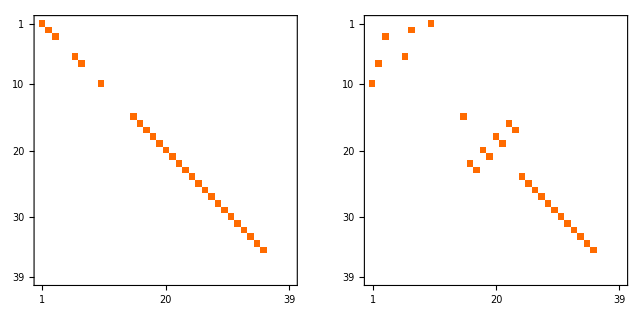

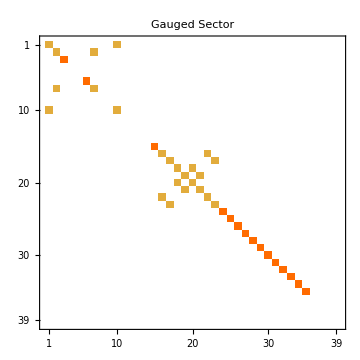

```mathematica
X = So . To;
Mv=DiagonalMatrix[Array[ηv[i[[#,1]]]ηv[i[[#,2]]](1-Abs[i[[#,3]]]-2)+ηv[i[[#,1]]]Abs[i[[#,3]]]-2&,{Length[i]}]];
Mvt= Chop[N[X† . Mv . X] ];
Mv'=So . Mv . So // FullSimplify;

Show[GraphicsRow[MapThread[Legended[MatrixPlot[#1,ImageSize->Full],Placed[#2,Below]]&,{{IdentityMatrix[Length[i]],Mv,Mv' ,Mvt },{"𝟙,𝟙","𝟙,η","η,𝟙","η,η"}}]],ImageSize->Full,PlotLabel->HoldForm["Individual Sectors"],LabelStyle->{GrayLevel[0]}]
GraphicsRow[{1/2(IdentityMatrix[Length[i]] + Mv) // MatrixPlot,1/2 Chop[(Mv' + Mvt)] // MatrixPlot}]
Mg = Chop[1/2(IdentityMatrix[Length[i]]  + Mv + Mv'+Mvt)];
MatrixPlot[Mg,PlotLabel->"Gauged Sector",ImageSize->Medium,LabelStyle->{GrayLevel[0]}]
```

```mathematica
(* Now Let's calculate the Partition Function *)
Xvt = Assuming[q>0,χvt[#,q,n]]&/@i;
Series[Chop[N[Xvt . Xvt]],{q,0,1}]//Echo[#,"Z_σ(q) = "]&;
Series[Chop[Xvt . Mg . Xvt],{q,0,1}]//Echo[#,"Z_(σ, η)(q) = "]&;
```

Z_σ(q) =   1/q^(7/60)+1/q^(1/24)+1/q^(7/240)+q^(1/120)+q^(1/30)+q^(17/240)+q^(1/12)+q^(19/120)+q^(17/60)+q^(49/120)+q^(137/240)+q^(91/120)+q^(5/6)+3. q^(23/24)+2. q^(233/240)+5. q^(121/120)+2. q^(31/30)+3. q^(257/240)+3. q^(13/12)+5. q^(139/120)+3. q^(77/60)+3. q^(169/120)+q^(353/240)+5. q^(377/240)+q^(49/30)+2. q^(211/120)+4. q^(11/6)+2. q^(113/60)+12. q^(47/24)+5. q^(473/240)+O[q]^2

Z_(σ, η)(q) =   1/q^(7/60)+2./q^(7/240)+2. q^(1/30)+2. q^(17/240)+q^(1/12)+q^(17/60)+2. q^(137/240)+2. q^(5/6)+4. q^(233/240)+4. q^(31/30)+6. q^(257/240)+3 q^(13/12)+6. q^(77/60)+2. q^(353/240)+10. q^(377/240)+2. q^(49/30)+8. q^(11/6)+2 q^(113/60)+10. q^(473/240)+O[q]^2

Now we can calculate if we have enough conformal weights to pullback modules

Here are the conformal weights for the gauged theory.

```mathematica
hg=ht/@i;

(* Now let's calculate the conformal weights of the Modules *)
hgM=Join@@(ConstantArray[Total[hg[[#]]&/@#[[1]]],Floor[#[[2]]]]&/@Most@ArrayRules[Mg]);
hcM= 2*hc;

(* We can print some stuff *)
Echo["","--------------- Chiral Modules ---------------"];
Echo[Sort[hg],"Gauged Chiral Weights: "];
Echo[Sort[hc],"Coset Chiral Weights: "];
Echo[Sort@DeleteDuplicates@Mod[hg,1],"Gauged Weights (mod 1): "];
Echo[Sort@DeleteDuplicates@Mod[hc,1],"Coset Weights (mod 1): "];
Echo["","---------------- Full Modules ----------------"];
Echo[Sort[hgM],"Gauged Module Weights: "];
Echo[Sort[hcM],"Coset Module Weights: "];
Echo[Sort@DeleteDuplicates@Mod[hgM,1],"Gauged Module Weights (mod 1): "];
Echo[Sort@DeleteDuplicates@Mod[hcM,1],"Coset Module Weights (mod 1): "];
```

--------------- Chiral Modules ---------------

Gauged Chiral Weights:   {0,3/80,7/160,1/16,3/40,3/32,1/10,11/80,1/5,21/80,11/32,7/16,19/40,43/80,87/160,9/16,19/32,3/5,51/80,7/10,61/80,127/160,27/32,7/8,1,83/80,43/40,6/5,6/5,207/160,3/2,123/80,8/5,15/8,31/16,21/10,11/5,3,4}

Coset Chiral Weights:   {0,7/160,7/160,3/40,3/40,3/32,3/32,1/10,1/5,11/32,11/32,19/40,19/40,19/32,19/32,3/5,7/10,7/10,127/160,127/160,27/32,27/32,7/8,7/8,43/40,43/40,6/5,207/160,207/160,3/2,3/2,247/160,247/160,15/8,15/8,2}

Gauged Weights (mod 1):   {0,3/80,7/160,1/16,3/40,3/32,1/10,11/80,1/5,21/80,47/160,11/32,7/16,19/40,1/2,43/80,87/160,9/16,19/32,3/5,51/80,7/10,61/80,127/160,27/32,7/8,15/16}

Coset Weights (mod 1):   {0,7/160,3/40,3/32,1/10,1/5,47/160,11/32,19/40,1/2,87/160,19/32,3/5,7/10,127/160,27/32,7/8}

---------------- Full Modules ----------------

Gauged Module Weights:   {0,7/80,7/80,3/20,3/20,3/16,3/16,1/5,2/5,11/16,11/16,19/20,19/20,87/80,87/80,19/16,19/16,6/5,7/5,7/5,7/5,7/5,127/80,127/80,27/16,27/16,7/4,7/4,2,43/20,43/20,11/5,11/5,11/5,11/5,12/5,12/5,207/80,207/80,3,3,3,3,16/5,17/5,17/5,15/4,15/4,21/5,22/5,5,5,6,8}

Coset Module Weights:   {0,7/80,7/80,3/20,3/20,3/16,3/16,1/5,2/5,11/16,11/16,19/20,19/20,19/16,19/16,6/5,7/5,7/5,127/80,127/80,27/16,27/16,7/4,7/4,43/20,43/20,12/5,207/80,207/80,3,3,247/80,247/80,15/4,15/4,4}

Gauged Module Weights (mod 1):   {0,7/80,3/20,3/16,1/5,2/5,47/80,11/16,3/4,19/20}

Coset Module Weights (mod 1):   {0,7/80,3/20,3/16,1/5,2/5,47/80,11/16,3/4,19/20}

Calculating pool for pullbacks
We want to create a list where for each module in the Coset theory which are the possible candidates for modules that it decomposes to in the gauged theory. To do this we are looking at which Gauged chiral module weights are at most an integer apart from the weight of the coset module.

```mathematica
candidates={#,Join@@Position[Mod[hgM,1],Mod[#,1]]}&/@hcM;
candidates //MatrixForm
```

(7/80 | {39,40,41,42}
3/20 | {31,32,33,34}
2/5 | {7,8,19,20,21,22,23,24,25,26}
3/16 | {43,44,45,46}
11/16 | {47,48,49,50}
11/16 | {47,48,49,50}
1/5 | {1,2,3,4,9,10,11,12}
19/20 | {13,14}
6/5 | {1,2,3,4,9,10,11,12}
19/20 | {13,14}
3/16 | {43,44,45,46}
19/16 | {43,44,45,46}
27/16 | {47,48,49,50}
27/16 | {47,48,49,50}
19/16 | {43,44,45,46}
3/20 | {31,32,33,34}
7/5 | {7,8,19,20,21,22,23,24,25,26}
43/20 | {31,32,33,34}
12/5 | {7,8,19,20,21,22,23,24,25,26}
43/20 | {31,32,33,34}
7/5 | {7,8,19,20,21,22,23,24,25,26}
7/80 | {39,40,41,42}
127/80 | {51,52,53,54}
207/80 | {51,52,53,54}
247/80 | {39,40,41,42}
247/80 | {39,40,41,42}
207/80 | {51,52,53,54}
127/80 | {51,52,53,54}
0 | {5,6,15,16,17,18,27,28,29,30}
7/4 | {35,36,37,38}
3 | {5,6,15,16,17,18,27,28,29,30}
15/4 | {35,36,37,38}
4 | {5,6,15,16,17,18,27,28,29,30}
15/4 | {35,36,37,38}
3 | {5,6,15,16,17,18,27,28,29,30}
7/4 | {35,36,37,38})

Now let’s check for the partition functions

```mathematica
XgM=Join@@(ConstantArray[Rationalize[Chop[N[Times@@(Xvt[[#]]&/@#[[1]])]]],Floor[#[[2]]]]&/@Most@ArrayRules[Mg]);
XcM=q^(2hw@@#-cw/12)χM[{#,#},q,χw,Floor[n-2hw@@#+cw/12+1]]&/@W;
(* It is now time to create previous list but with the partition function *)
candidateCharacters=Array[{q^(cw/12-candidates[[#,1]])XcM[[#]],q^(cw/12-candidates[[#,1]])XgM[[candidates[[#,2]]]]}&,{Length[candidates]}];
(* Let's fix the system such that there are positive powers of q on each side *)
candidateCharactersModified=MapThread[q^-#2#1&,{candidateCharacters,Min[Exponent[#,q,Min]&/@#[[2]]]& /@candidateCharacters}];
(* Now solve for the Character pullbacks *)
linearSolutions=Quiet@Check[LinearSolve[Transpose[CoefficientList[#,q,n]&@#[[2]]],CoefficientList[#[[1]],q,n]],{},LinearSolve::nosol]&/@candidateCharactersModified;
solutions=Array[{hcM[[#]],Map[Function[x,{x[[2]],hgM[[candidates[[#,2,x[[1,1]]]]]]}],(Most@ArrayRules@(linearSolutions[[#]]))]}&,{Length[linearSolutions]}];
Row[{candidates//MatrixForm,Array[{hcM[[#]],linearSolutions[[#]]}&,{Length[linearSolutions]}]//MatrixForm,solutions//MatrixForm}]
```

(7/80 | {39,40,41,42}
3/20 | {31,32,33,34}
2/5 | {7,8,19,20,21,22,23,24,25,26}
3/16 | {43,44,45,46}
11/16 | {47,48,49,50}
11/16 | {47,48,49,50}
1/5 | {1,2,3,4,9,10,11,12}
19/20 | {13,14}
6/5 | {1,2,3,4,9,10,11,12}
19/20 | {13,14}
3/16 | {43,44,45,46}
19/16 | {43,44,45,46}
27/16 | {47,48,49,50}
27/16 | {47,48,49,50}
19/16 | {43,44,45,46}
3/20 | {31,32,33,34}
7/5 | {7,8,19,20,21,22,23,24,25,26}
43/20 | {31,32,33,34}
12/5 | {7,8,19,20,21,22,23,24,25,26}
43/20 | {31,32,33,34}
7/5 | {7,8,19,20,21,22,23,24,25,26}
7/80 | {39,40,41,42}
127/80 | {51,52,53,54}
207/80 | {51,52,53,54}
247/80 | {39,40,41,42}
247/80 | {39,40,41,42}
207/80 | {51,52,53,54}
127/80 | {51,52,53,54}
0 | {5,6,15,16,17,18,27,28,29,30}
7/4 | {35,36,37,38}
3 | {5,6,15,16,17,18,27,28,29,30}
15/4 | {35,36,37,38}
4 | {5,6,15,16,17,18,27,28,29,30}
15/4 | {35,36,37,38}
3 | {5,6,15,16,17,18,27,28,29,30}
7/4 | {35,36,37,38})(7/80 | {1,0,0,0}
3/20 | {1,0,0,0}
2/5 | {0,0,1,2,0,0,0,1,0,0}
3/16 | {1,0,0,0}
11/16 | {}
11/16 | {}
1/5 | {1,2,0,0,0,0,0,1}
19/20 | {1,0}
6/5 | {}
19/20 | {1,0}
3/16 | {1,0,0,0}
19/16 | {}
27/16 | {}
27/16 | {}
19/16 | {}
3/20 | {1,0,0,0}
7/5 | {}
43/20 | {}
12/5 | {}
43/20 | {}
7/5 | {}
7/80 | {1,0,0,0}
127/80 | {}
207/80 | {}
247/80 | {}
247/80 | {}
207/80 | {}
127/80 | {}
0 | {0,0,1,2,0,0,0,1,0,0}
7/4 | {}
3 | {}
15/4 | {}
4 | {}
15/4 | {}
3 | {}
7/4 | {})(7/80 | {{1,7/80}}
3/20 | {{1,3/20}}
2/5 | {{1,2/5},{2,7/5},{1,12/5}}
3/16 | {{1,3/16}}
11/16 | {}
11/16 | {}
1/5 | {{1,1/5},{2,11/5},{1,21/5}}
19/20 | {{1,19/20}}
6/5 | {}
19/20 | {{1,19/20}}
3/16 | {{1,3/16}}
19/16 | {}
27/16 | {}
27/16 | {}
19/16 | {}
3/20 | {{1,3/20}}
7/5 | {}
43/20 | {}
12/5 | {}
43/20 | {}
7/5 | {}
7/80 | {{1,7/80}}
127/80 | {}
207/80 | {}
247/80 | {}
247/80 | {}
207/80 | {}
127/80 | {}
0 | {{1,0},{2,3},{1,6}}
7/4 | {}
3 | {}
15/4 | {}
4 | {}
15/4 | {}
3 | {}
7/4 | {})